# Data preprocessing: SMD data set NANOG and GATA6

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
baseDirectory=StringReplace[ParentDirectory[NotebookDirectory[]],"dataPreprocessing"->"analysisCode"];
```

```mathematica
<<(FileNameJoin[{baseDirectory,"CellNucleiSegmentation_v8.m"}]) (*code from Schmitz et al. Scientific Reports 2017*)
```

```mathematica
<<(FileNameJoin[{baseDirectory,"neighbourAnaFunctions_v2.m"}])(*code from Fischer et al. PLOS One 2020 and extensions*)
```

```mathematica
shiftValue[expName_,val_,setThresholdIndex_,threshold_,experiments_]:=Block[{index},index=expName/.experiments;
val+(threshold[[setThresholdIndex]]-threshold[[index]])]
```

```mathematica
zCorrection[fileName_,slope_,channels_:{"Dapi","Nanog","Gata6","Gata4"}]:=Block[{nucleiFeatures,nucleiFeaturesWithCorr,exportFName},
nucleiFeatures="NucleiFeatures"/.Import[fileName];
nucleiFeaturesWithCorr=Join[#,
Table[channels[[i]]<>"-AvgLnCorr"->Log[channels[[i]]<>"-Avg"/.#]-slope[[i]]*("Centroid"/.#)[[3]],{i,1,Length[channels]}]&@#]&/@nucleiFeatures;
exportFName=StringReplace[fileName,"Features.mx"->"Features_ZCorrected.mx"];
Export[exportFName,"NucleiFeatures"->nucleiFeaturesWithCorr]
]
```

```mathematica
fontOption="Arial";
```

```mathematica
<<ErrorBarPlots`
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
plotMeanStdLighter[xValues_,yValues_,smooth_,xLabel_,yLabel_,colour_]:=
Show[Table[ListLinePlot[{Transpose[{xValues[[i]],MeanFilter[#[[All,1]]+#[[All,2]],smooth]}],
Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]}&@yValues[[i]],PlotRange->{0,All},
PlotStyle->{Directive[Opacity[0.5],Lighter[colour[i],0.7]],Directive[Opacity[0.5],Lighter[colour[i],0.7]]},Filling->1->{2},FillingStyle->Directive[Opacity[0.5],Lighter[colour[i],0.5]],Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{xLabel,yLabel}],{i,1,Length[xValues]}],
ListLinePlot[Table[Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]],{i,1,Length[xValues]}],
PlotRange->{0,All},PlotStyle->Transpose[{ConstantArray[Thickness[0.007],Length[xValues]],Table[colour[i],{i,1,Length[xValues]}]}],Frame->{True,True,None,None},FrameStyle->Directive[Black,FontFamily->fontOption,14],FrameLabel->{xLabel,yLabel}]]
```

```mathematica
smoothedValues[unsmoothedData_,smooth_]:=Block[{xValues,yValues,lowerLimit,mean},
xValues=#[[All,1]]&/@unsmoothedData;
yValues=#[[All,2;;3]]&/@unsmoothedData;
Table[lowerLimit=Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]&@yValues[[i]];mean=Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]];Table[Join[mean[[i]],{(mean-lowerLimit)[[i,-1]]}],{i,1,Length[mean]}],{i,1,Length[xValues]}]
]
```

```mathematica
colourNegPos[i_]:={Lighter[Gray,0.3],Darker[Gray,0.7]}[[i]]
```

```mathematica
colour3[i_]:=Join[{Darker[Gray]},(ColorData[16]/@{3,6,4})][[i]]
```

```mathematica
colour2[i_]:={Darker[Gray],Darker[Purple],Darker[Green,0.7]}[[i]]
```

```mathematica
colour1[i_]:={Darker[Gray],Darker[Purple],Darker[Green,0.7],Darker[Cyan,0.5]}[[i]]
```

```mathematica
populationsColours={Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]};
```

## Converting data from MINS

renaming channels, tissue classification and rescaling of centroid position to µm

### Experiment CD1-DapiB-Gata6G-TotalR-NanogM.mdb

```mathematica
fNames=FileNames["*TotalR*",FileNameJoin[{NotebookDirectory[],"DataFromMINS"}]];
```

```mathematica
convertFromMINS[#,StringReplace[(StringTake[#,StringPosition[#,"_cha"][[1,1]]-1]<>"_Features.mx"),"DataFromMINS"->"EmbryoFeatures"],"ImagingChannels"->{"CH1-Avg"->"Dapi-Avg","CH1-Sum"->"Dapi-Sum","CH2-Avg"->"Brightfield-Avg","CH2-Sum"->"Brightfield-Sum","CH3-Avg"->"Gata6-Avg","CH3-Sum"->"Gata6-Sum","CH4-Avg"->"TotalBC-Avg","CH4-Sum"->"TotalBC-Sum","CH5-Avg"->"Nanog-Avg","CH5-Sum"->"Nanog-Sum"}]&/@fNames;
```

### Experiment CD1-DapiB-Gata6-YapR-NanogM260315.mdb

```mathematica
fNames=FileNames["*YapR*",FileNameJoin[{NotebookDirectory[],"DataFromMINS"}]];
```

```mathematica
convertFromMINS[#,StringReplace[(StringTake[#,StringPosition[#,"_cha"][[1,1]]-1]<>"_Features.mx"),"DataFromMINS"->"EmbryoFeatures"],"ImagingChannels"->{"CH1-Avg"->"Dapi-Avg","CH1-Sum"->"Dapi-Sum","CH2-Avg"->"Brightfield-Avg","CH2-Sum"->"Brightfield-Sum","CH3-Avg"->"Gata6-Avg","CH3-Sum"->"Gata6-Sum","CH4-Avg"->"Yap-Avg","CH4-Sum"->"Yap-Sum","CH5-Avg"->"Nanog-Avg","CH5-Sum"->"Nanog-Sum"}]&/@fNames;
```

### Experiment Excel files embryo Gata6 Nanog ABC

```mathematica
fNames=FileNames["*ABC*",FileNameJoin[{NotebookDirectory[],"DataFromMINS"}]];
```

```mathematica
convertFromMINS[#,StringReplace[(StringTake[#,StringPosition[#,"_cha"][[1,1]]-1]<>"_Features.mx"),"DataFromMINS"->"EmbryoFeatures"]]&/@fNames;
```

## z-Correction

Use TE cells to determine curve for correction, do natural logarithm and linear fit (motivated by Saiz et al 2016) per experiment, per channel

The DAPI channel looks dimmer as in other data. Also the actual gain and laser intensities changed slightly. But since we do one z-correction/channel it does not matter.

#### CD1-DapiB-Gata6G-TotalR-NanogM.mdb (Batch 1)

```mathematica
featuresFNamesRaw=FileNames["*TotalR*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
fNamesBatch4=Join[Select[featuresFNamesRaw,StringContainsQ[#,"embryo14a"]&],Select[featuresFNamesRaw,StringContainsQ[#,"embryo15a"]&]]
```

```mathematica
featuresFNames=Complement[featuresFNamesRaw,fNamesBatch4];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
nucleiFeatures[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Brightfield-Avg,Brightfield-Sum,Gata6-Avg,Gata6-Sum,TotalBC-Avg,TotalBC-Sum,Nanog-Avg,Nanog-Sum}

```mathematica
zAndExprPerEmbryo=Table[{#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@({"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures[[i]]),{i,1,Length[nucleiFeatures]}];
```

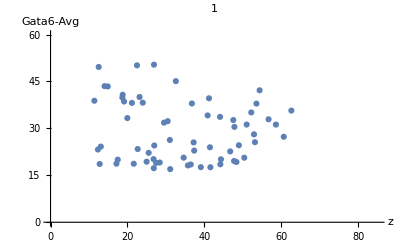
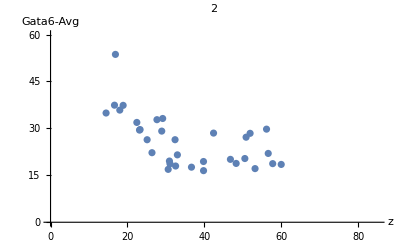
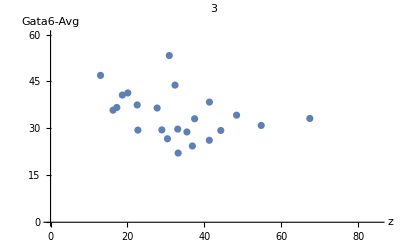
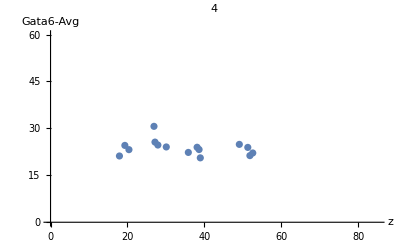
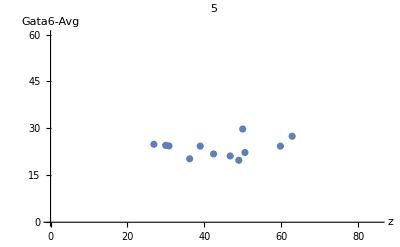
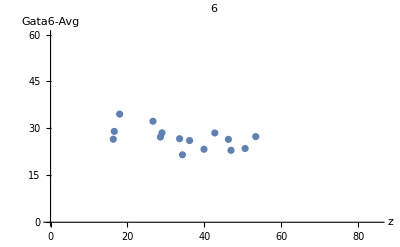
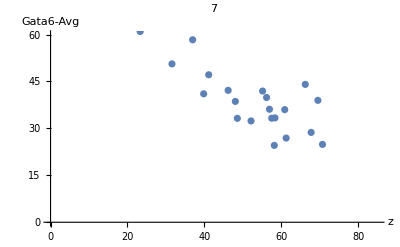
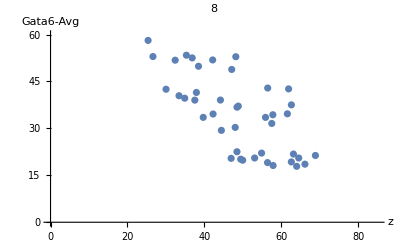

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,4}]],PlotRange->{{0,85},{0,60}},AxesLabel->{"z","Gata6-Avg"},PlotLabel->ToString[i]],{i,1,Length[zAndExprPerEmbryo]}]
```

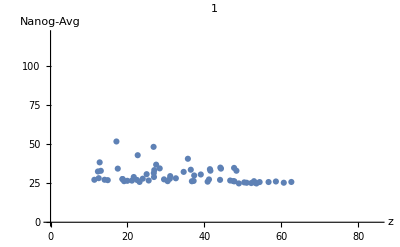
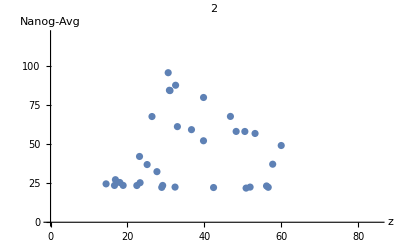
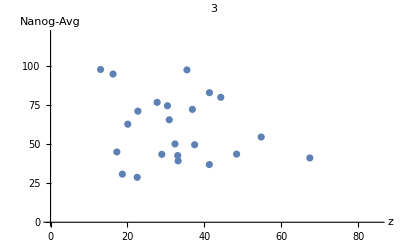
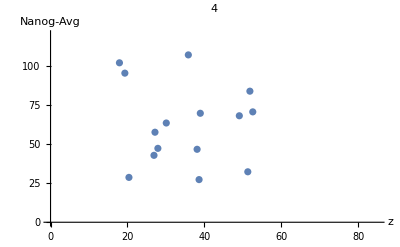
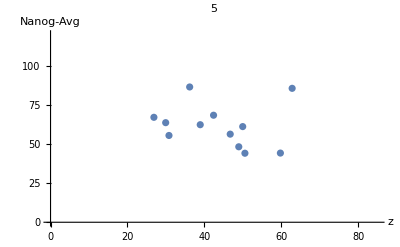
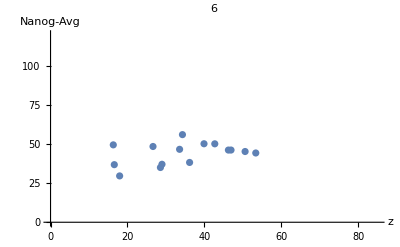
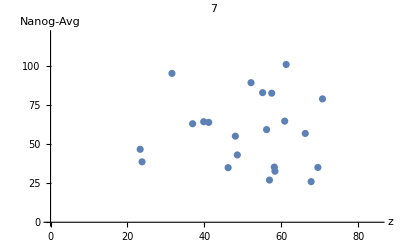
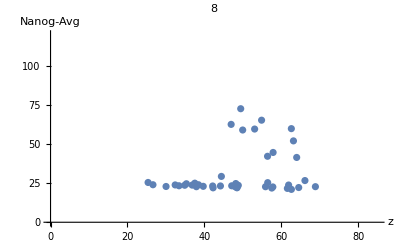

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,3}]],PlotRange->{{0,85},{0,120}},AxesLabel->{"z","Nanog-Avg"},PlotLabel->ToString[i]],{i,1,Length[zAndExprPerEmbryo]}]
```

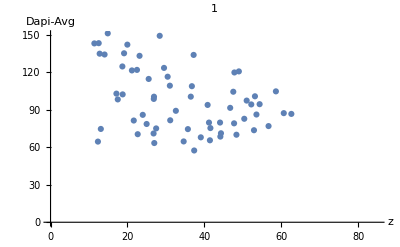
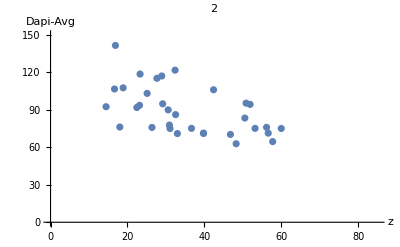
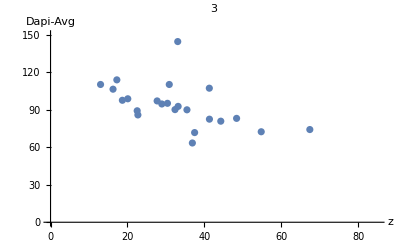
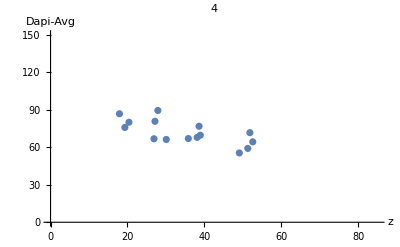
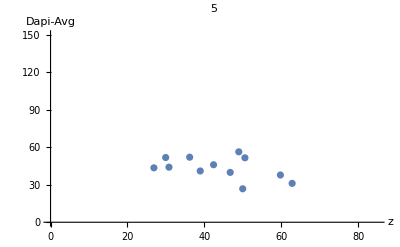
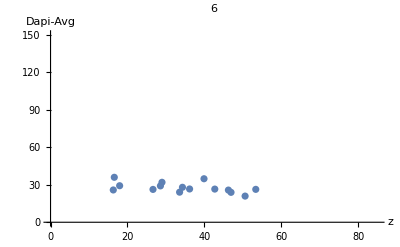
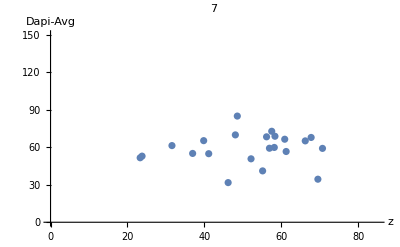
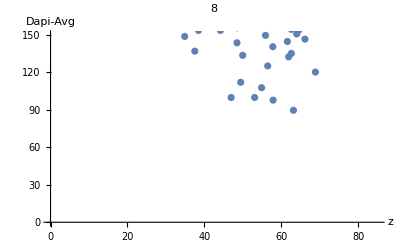

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,2}]],PlotRange->{{0,85},{0,150}},AxesLabel->{"z","Dapi-Avg"},PlotLabel->ToString[i]],{i,1,Length[zAndExprPerEmbryo]}]
```

```mathematica
TableForm[Transpose[{Range[Length[featuresFNames]],FileBaseName/@featuresFNames}]]
```

1 | CD1-DapiB-Gata6G-TotalRa-NanogM-embryo11_Features
2 | CD1-DapiB-Gata6G-TotalRa-NanogM-embryo18b_Features
3 | CD1-DapiB-Gata6G-TotalRa-NanogM-embryo20b_Features
4 | CD1-DapiB-Gata6G-TotalRa-NanogM-embryo21b_Features
5 | CD1-DapiB-Gata6G-TotalRa-NanogM-embryo22b_Features
6 | CD1-DapiB-Gata6G-TotalR-NanogM-embryo10_Features
7 | CD1-DapiB-Gata6G-TotalR-NanogM-embryo1_Features
8 | CD1-DapiB-Gata6G-TotalR-NanogM-embryo2_Features
9 | CD1-DapiB-Gata6G-TotalR-NanogM-embryo3_Features
10 | CD1-DapiB-Gata6G-TotalR-NanogM-embryo4_Features
11 | CD1-DapiB-Gata6G-TotalR-NanogM-embryo5_Features
12 | CD1-DapiB-Gata6G-TotalR-NanogM-embryo6_Features
13 | CD1-DapiB-Gata6G-TotalR-NanogM-embryo7_Features
14 | CD1-DapiB-Gata6G-TotalR-NanogM-embryo8_Features
15 | CD1-DapiB-Gata6G-TotalR-NanogM-embryo9_Features

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures,1];
```

```mathematica
zAndExprTE=Select[zAndExpr,#[[-1]]=="TE"&];
```

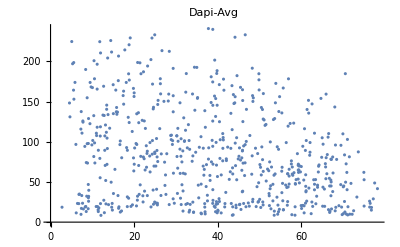
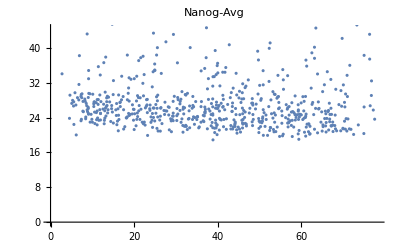
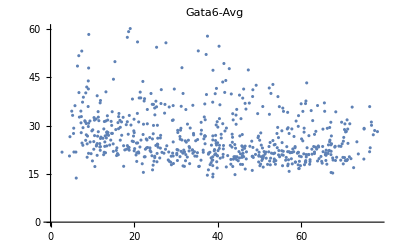

```mathematica
Table[ListPlot[zAndExprTE[[All,{1,i}]],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

```mathematica
lmLnTR=Table[LinearModelFit[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],x,x],{i,{2,3,4}}]
```

{FittedModel[4.46765-0.00918229 x],FittedModel[3.31712-0.000599692 x],FittedModel[3.37579-0.00354657 x]}

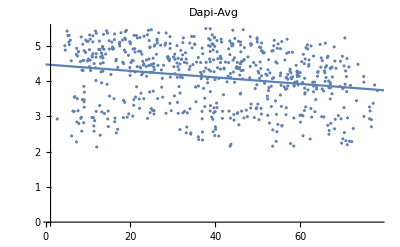
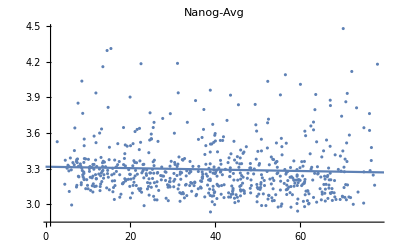
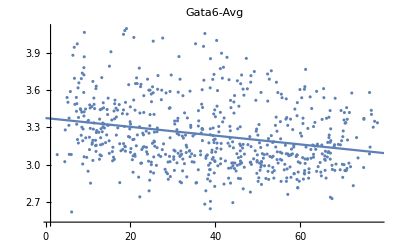

```mathematica
Table[Show[ListPlot[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],PlotRange->All],Plot[lmLnTR[[i-1]][x],{x,0,90}],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

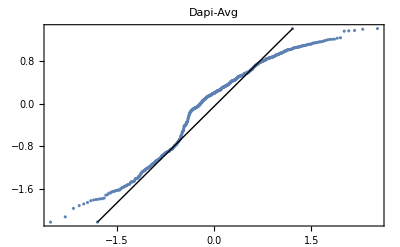
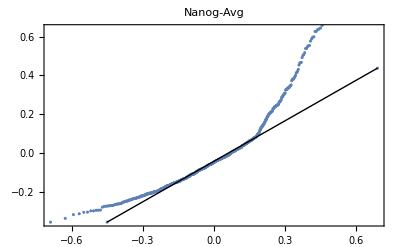
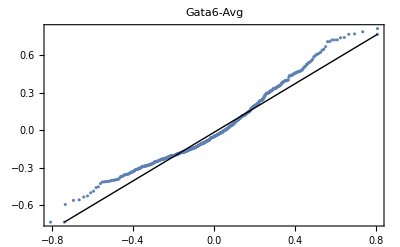

```mathematica
Table[QuantilePlot[lmLnTR[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

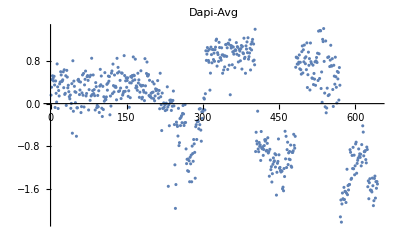
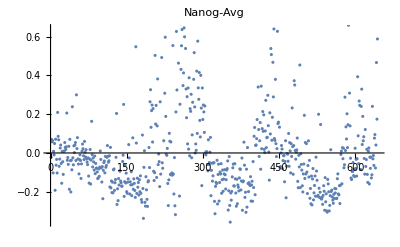
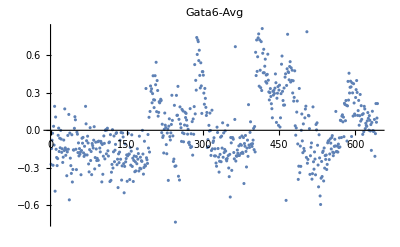

```mathematica
Table[ListPlot[lmLnTR[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

```mathematica
slopeTR=Table[lmLnTR[[i]]["BestFitParameters"][[2]],{i,1,Length[lmLnTR]}]
```

{-0.00918229,-0.000599692,-0.00354657}

corrected values

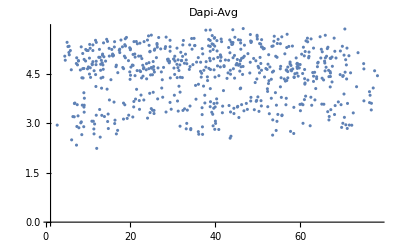
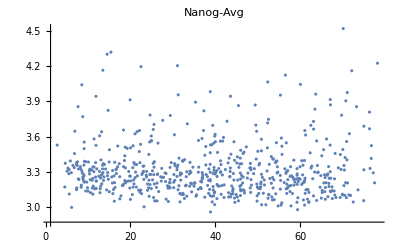
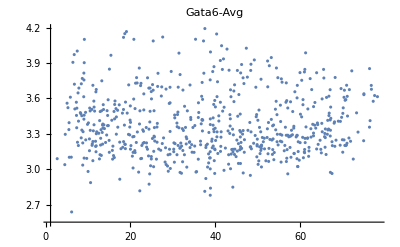

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slopeTR[[i-1]]*#[[1]]})&/@zAndExprTE[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

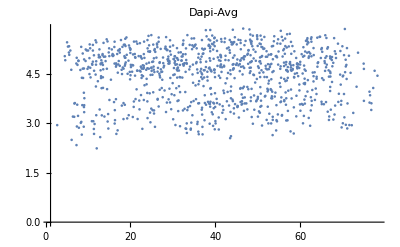
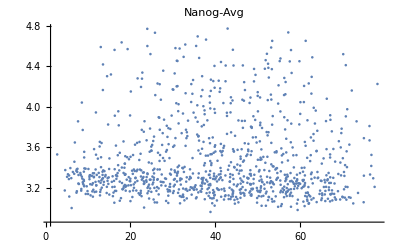
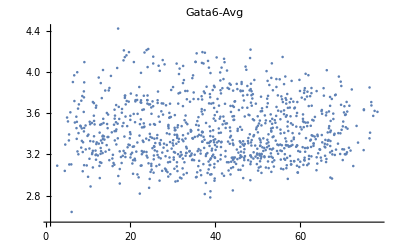

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slopeTR[[i-1]]*#[[1]]})&/@zAndExpr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

Export corrected values for Batch 1

```mathematica
zCorrection[#,slopeTR,{"Dapi","Nanog","Gata6"}]&/@featuresFNames;
```

Test

```mathematica
corrFeaturesFNames=FileNames["*TotalR*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeaturesZCorr=("NucleiFeatures"/.Import[#])&/@corrFeaturesFNames;
```

```mathematica
nucleiFeaturesZCorr[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Brightfield-Avg,Brightfield-Sum,Gata6-Avg,Gata6-Sum,TotalBC-Avg,TotalBC-Sum,Nanog-Avg,Nanog-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr}

```mathematica
zAndExprZCorr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","TE/ICM"}/.nucleiFeaturesZCorr,1];
```

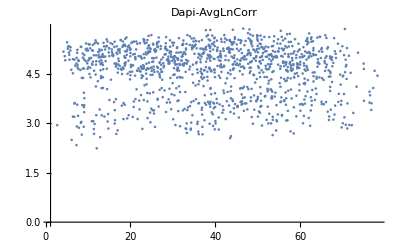
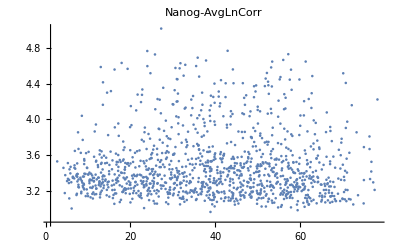
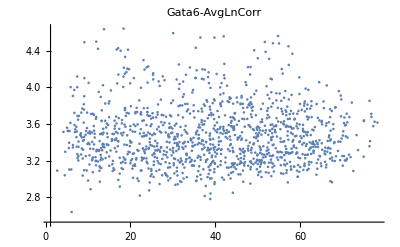

```mathematica
Table[ListPlot[zAndExprZCorr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}[[i-1]]],{i,{2,3,4}}]
```

#### CD1-DapiB-Gata6-YapR-NanogM260315.mdb (Batch 2)

```mathematica
featuresFNames=FileNames["*YapR*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
nucleiFeatures
```

{{{Inlier/Outlier→1,EmbryoId→1,CellID→1,Size→213.442,TE/ICM→TE,Centroid→{102.475,84.2456,3.4159},Dapi-Avg→182.92,Dapi-Sum→250000.,Brightfield-Avg→123.99,Brightfield-Sum→170000.,Gata6-Avg→6.5351,Gata6-Sum→8940,Yap-Avg→27.05,Yap-Sum→37005,Nanog-Avg→13.699,Nanog-Sum→18740},138,{Inlier/Outlier→1,EmbryoId→1,CellID→149,Size→311.27,TE/ICM→TE,Centroid→{101.681,73.5253,76.833},Dapi-Avg→49.55,Dapi-Sum→98852,Brightfield-Avg→129.29,Brightfield-Sum→258000.,Gata6-Avg→11.733,Gata6-Sum→23408,Yap-Avg→25.364,Yap-Sum→50601,Nanog-Avg→10.042,Nanog-Sum→20034}},8,{{Inlier/Outlier→1,EmbryoId→1,CellID→1,10,Yap-Sum→79780,Nanog-Avg→14.46,Nanog-Sum→31654},55,{1}}}
 |  |  |  |

```mathematica
nucleiFeatures[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Brightfield-Avg,Brightfield-Sum,Gata6-Avg,Gata6-Sum,Yap-Avg,Yap-Sum,Nanog-Avg,Nanog-Sum}

```mathematica
zAndExprPerEmbryo=Table[{#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@({"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures[[i]]),{i,1,Length[nucleiFeatures]}];
```

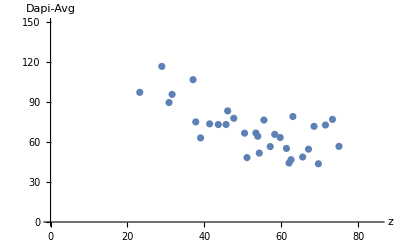
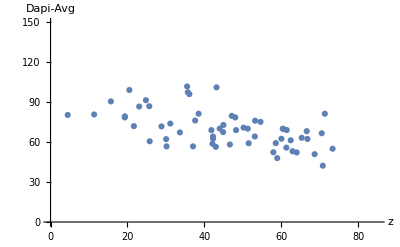
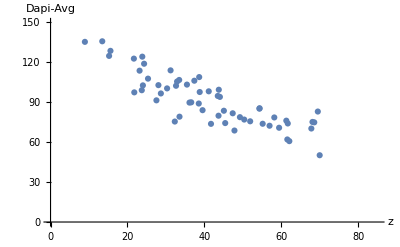
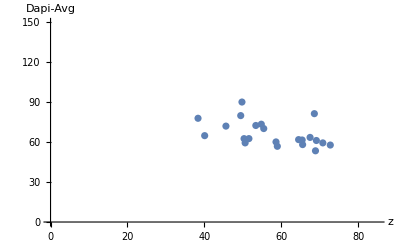
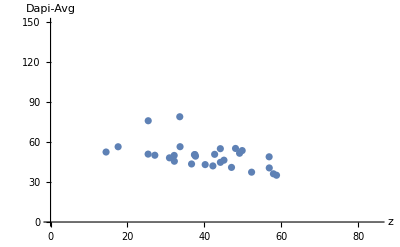
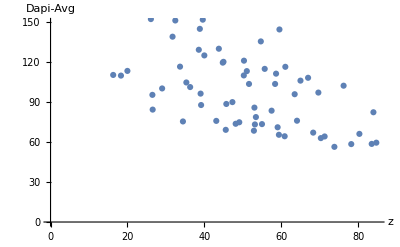
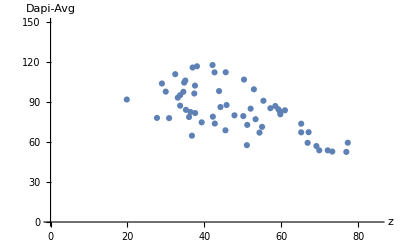
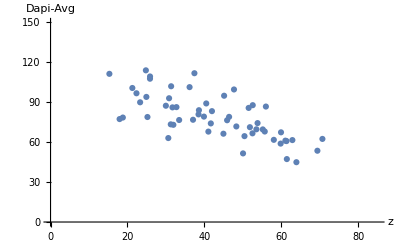

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,2}]],PlotRange->{{0,85},{0,150}},AxesLabel->{"z","Dapi-Avg"}],{i,1,Length[zAndExprPerEmbryo]}]
```

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures,1];
```

```mathematica
zAndExprTE=Select[zAndExpr,#[[-1]]=="TE"&];
```

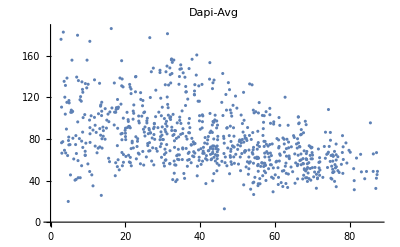
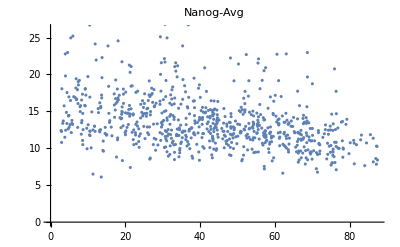
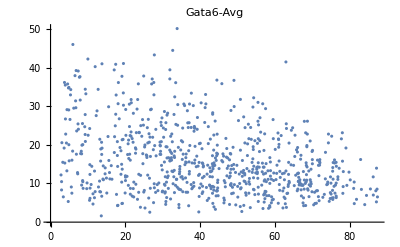

```mathematica
Table[ListPlot[zAndExprTE[[All,{1,i}]],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

```mathematica
lmLnYR=Table[LinearModelFit[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],x,x],{i,{2,3,4}}]
```

{FittedModel[4.63807-0.00745337 x],FittedModel[2.81286-0.00483473 x],FittedModel[2.95533-0.00800009 x]}

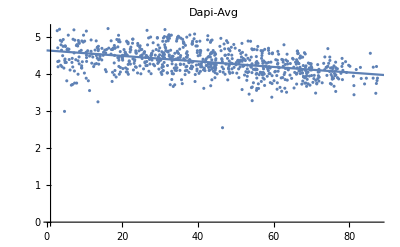
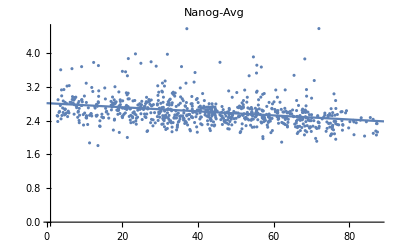
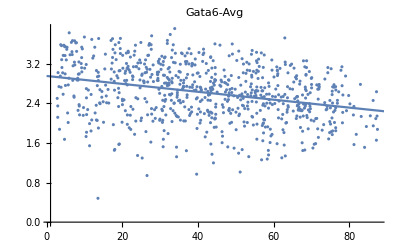

```mathematica
Table[Show[ListPlot[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],PlotRange->All],Plot[lmLnYR[[i-1]][x],{x,0,90}],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

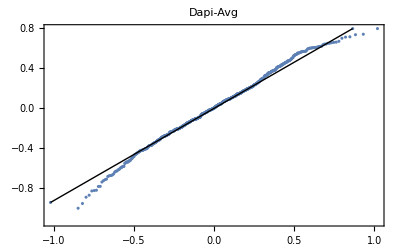
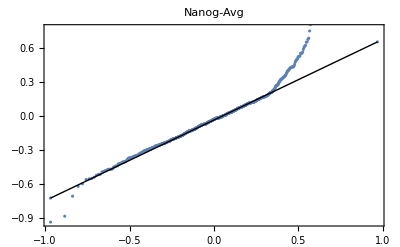
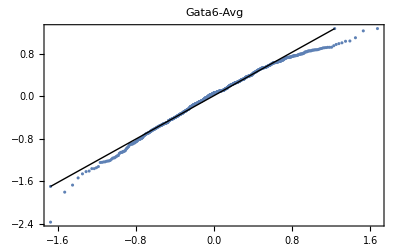

```mathematica
Table[QuantilePlot[lmLnYR[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

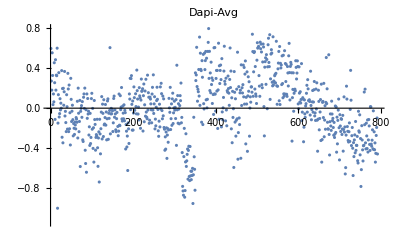
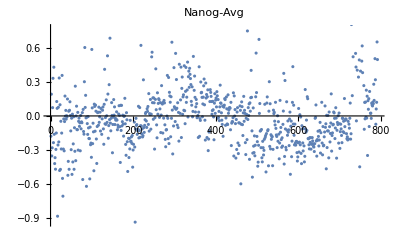
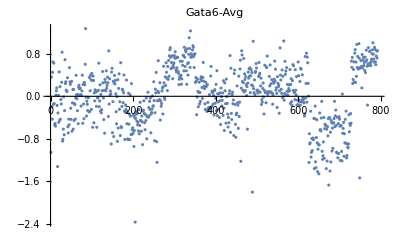

```mathematica
Table[ListPlot[lmLnYR[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

```mathematica
slopeYR=Table[lmLnYR[[i]]["BestFitParameters"][[2]],{i,1,Length[lmLnYR]}]
```

{-0.00745337,-0.00483473,-0.00800009}

corrected values

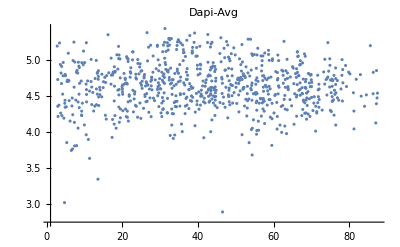
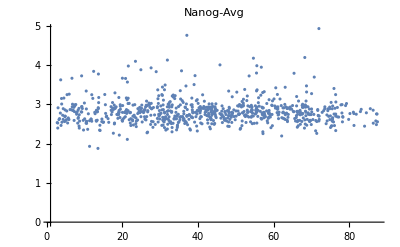
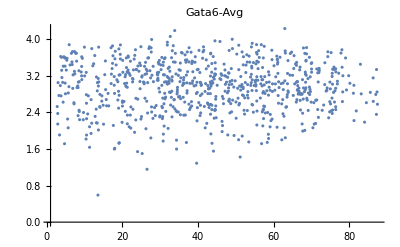

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slopeYR[[i-1]]*#[[1]]})&/@zAndExprTE[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

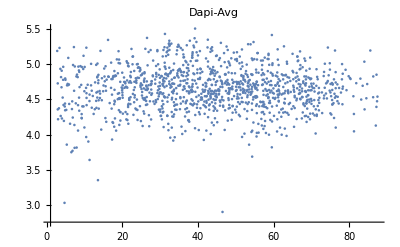
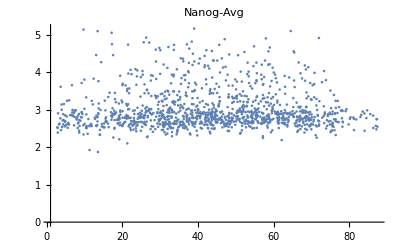
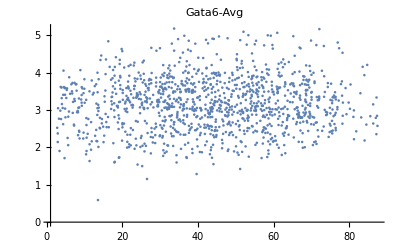

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slopeYR[[i-1]]*#[[1]]})&/@zAndExpr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

Export corrected values for 27

```mathematica
zCorrection[#,slopeYR,{"Dapi","Nanog","Gata6"}]&/@featuresFNames;
```

Test

```mathematica
corrFeaturesFNames=FileNames["*YapR*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeaturesZCorr=("NucleiFeatures"/.Import[#])&/@corrFeaturesFNames;
```

```mathematica
nucleiFeaturesZCorr[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Brightfield-Avg,Brightfield-Sum,Gata6-Avg,Gata6-Sum,Yap-Avg,Yap-Sum,Nanog-Avg,Nanog-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr}

```mathematica
zAndExprZCorr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr","TE/ICM"}/.nucleiFeaturesZCorr,1];
```

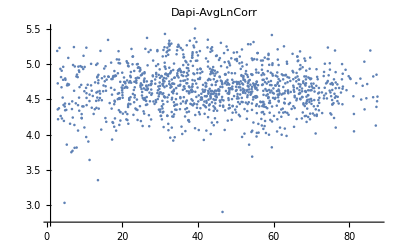
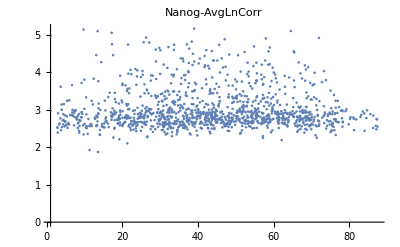
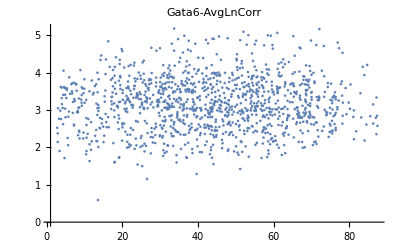

```mathematica
Table[ListPlot[zAndExprZCorr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}[[i-1]]],{i,{2,3,4}}]
```

#### Excel files embryo Gata6 Nanog ABC (Batch 3)

```mathematica
featuresFNames=FileNames["*ABC*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
featuresFNames[[{6,12,13,17}]]
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
nucleiFeatures[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Brightfield-Avg,Brightfield-Sum,Gata6-Avg,Gata6-Sum,ABC-Avg,ABC-Sum,Nanog-Avg,Nanog-Sum}

```mathematica
zAndExprPerEmbryo=Table[{#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@({"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures[[i]]),{i,1,Length[nucleiFeatures]}];
```

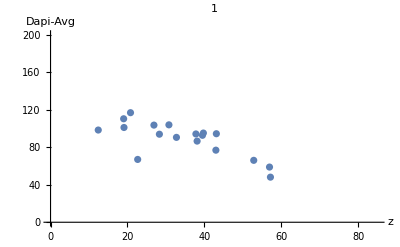
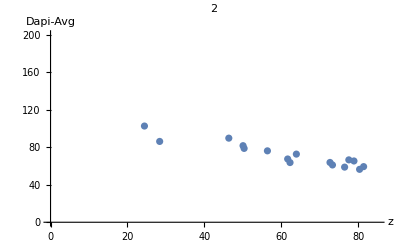
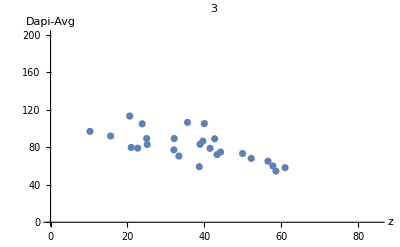
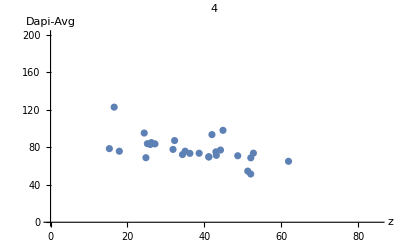
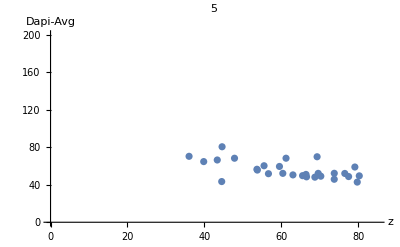
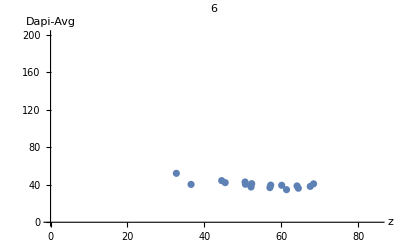
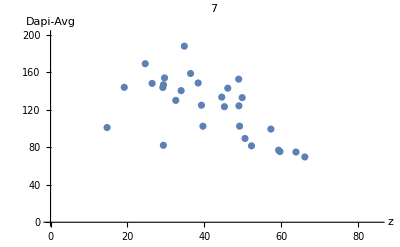
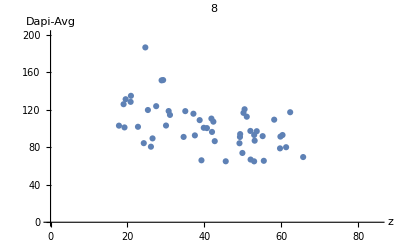

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,2}]],PlotRange->{{0,85},{0,200}},AxesLabel->{"z","Dapi-Avg"},PlotLabel->ToString[i]],{i,1,Length[zAndExprPerEmbryo]}]
```

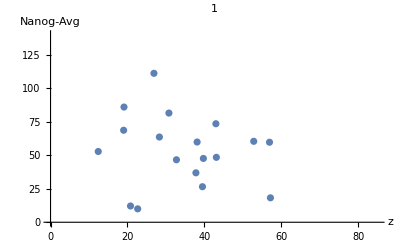
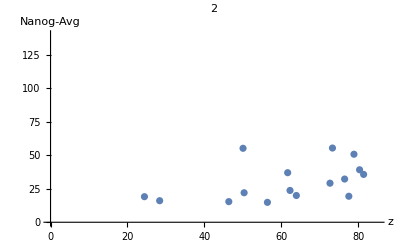
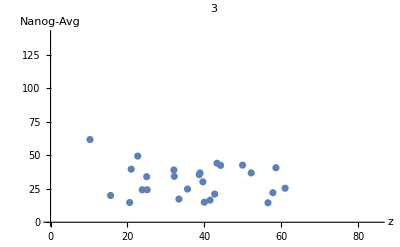
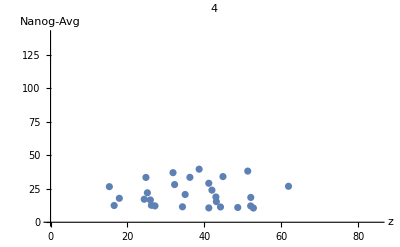
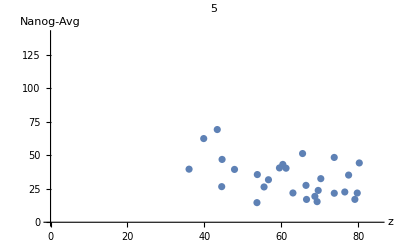
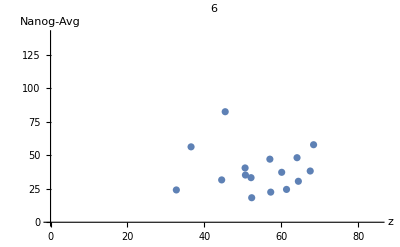
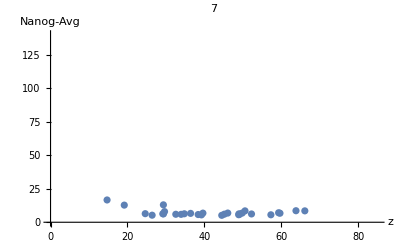
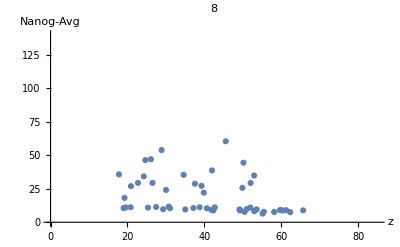
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,3}]],PlotRange->{{0,85},{0,140}},AxesLabel->{"z","Nanog-Avg"},PlotLabel->ToString[i]],{i,1,Length[zAndExprPerEmbryo]}]
```

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,4}]],PlotRange->{{0,85},{0,70}},AxesLabel->{"z","Gata6-Avg"},PlotLabel->ToString[i]],{i,1,Length[zAndExprPerEmbryo]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TableForm[Transpose[{Range[Length[featuresFNames]],FileBaseName/@featuresFNames}]]
```

1 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoA_Features
2 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoC_Features
3 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoF_Features
4 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoG_Features
5 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoH_Features
6 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoI_Features
7 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoM_Features
8 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoN_Features
9 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoO_Features
10 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoP_Features
11 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoQ_Features
12 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoR_Features
13 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoS_Features
14 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoT_Features
15 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoU_Features
16 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoV_Features
17 | CD1-DapiB-Gata6G-ABCr-NanogM-embryoW_Features

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures,1];
```

```mathematica
zAndExprTE=Select[zAndExpr,#[[-1]]=="TE"&];
```

```mathematica
Table[ListPlot[zAndExprTE[[All,{1,i}]],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
lmLnABC=Table[LinearModelFit[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],x,x],{i,{2,3,4}}]
```

{FittedModel[4.60921-0.00980963 x],FittedModel[2.36555-0.00314295 x],FittedModel[3.39902-0.00529336 x]}

```mathematica
Table[Show[ListPlot[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],PlotRange->All],Plot[lmLnABC[[i-1]][x],{x,0,90}],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[QuantilePlot[lmLnABC[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[lmLnABC[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
slopeABC=Table[lmLnABC[[i]]["BestFitParameters"][[2]],{i,1,Length[lmLnABC]}]
```

{-0.00980963,-0.00314295,-0.00529336}

corrected values

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slopeABC[[i-1]]*#[[1]]})&/@zAndExprTE[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slopeABC[[i-1]]*#[[1]]})&/@zAndExpr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

Export corrected values for Batch 3

```mathematica
zCorrection[#,slopeABC,{"Dapi","Nanog","Gata6"}]&/@featuresFNames;
```

Test

```mathematica
corrFeaturesFNames=FileNames["*ABC*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeaturesZCorr=("NucleiFeatures"/.Import[#])&/@corrFeaturesFNames;
```

```mathematica
nucleiFeaturesZCorr[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Brightfield-Avg,Brightfield-Sum,Gata6-Avg,Gata6-Sum,ABC-Avg,ABC-Sum,Nanog-Avg,Nanog-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr}

```mathematica
zAndExprZCorr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","TE/ICM"}/.nucleiFeaturesZCorr,1];
```

```mathematica
Table[ListPlot[zAndExprZCorr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

#### CD1-DapiB-Gata6G-TotalR-NanogM.mdb, embryos 14a und 15a (Batch 4)

```mathematica
featuresFNamesRaw=FileNames["*TotalR*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
featuresFNames=Join[Select[featuresFNamesRaw,StringContainsQ[#,"embryo14a"]&],Select[featuresFNamesRaw,StringContainsQ[#,"embryo15a"]&]]
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
nucleiFeatures[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Brightfield-Avg,Brightfield-Sum,Gata6-Avg,Gata6-Sum,TotalBC-Avg,TotalBC-Sum,Nanog-Avg,Nanog-Sum}

```mathematica
zAndExprPerEmbryo=Table[{#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@({"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures[[i]]),{i,1,Length[nucleiFeatures]}];
```

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,2}]],PlotRange->{{0,85},{0,All}},AxesLabel->{"z","Dapi-Avg"}],{i,1,Length[zAndExprPerEmbryo]}]
```

{-Graphics-,-Graphics-}

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures,1];
```

```mathematica
zAndExprTE=Select[zAndExpr,#[[-1]]=="TE"&];
```

```mathematica
Table[ListPlot[zAndExprTE[[All,{1,i}]],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
lmLnB4=Table[LinearModelFit[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],x,x],{i,{2,3,4}}]
```

{FittedModel[5.10087-0.0102511 x],FittedModel[3.46642-0.00291215 x],FittedModel[3.54966-0.0061784 x]}

```mathematica
Table[Show[ListPlot[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],PlotRange->All],Plot[lmLnB4[[i-1]][x],{x,0,90}],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[QuantilePlot[lmLnB4[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[lmLnB4[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
slopeB4=Table[lmLnB4[[i]]["BestFitParameters"][[2]],{i,1,Length[lmLnB4]}]
```

{-0.0102511,-0.00291215,-0.0061784}

corrected values

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slopeB4[[i-1]]*#[[1]]})&/@zAndExprTE[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slopeB4[[i-1]]*#[[1]]})&/@zAndExpr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

Export corrected values for Batch 4

```mathematica
zCorrection[#,slopeB4,{"Dapi","Nanog","Gata6"}]&/@featuresFNames;
```

Test

```mathematica
corrFeaturesFNamesRaw=FileNames["*TotalR*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
corrFeaturesFNames=Join[Select[corrFeaturesFNamesRaw,StringContainsQ[#,"embryo14a"]&],Select[corrFeaturesFNamesRaw,StringContainsQ[#,"embryo15a"]&]]
```

```mathematica
nucleiFeaturesZCorr=("NucleiFeatures"/.Import[#])&/@corrFeaturesFNames;
```

```mathematica
nucleiFeaturesZCorr[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Brightfield-Avg,Brightfield-Sum,Gata6-Avg,Gata6-Sum,TotalBC-Avg,TotalBC-Sum,Nanog-Avg,Nanog-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr}

```mathematica
zAndExprZCorr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","TE/ICM"}/.nucleiFeaturesZCorr,1];
```

```mathematica
Table[ListPlot[zAndExprZCorr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}[[i-1]]],{i,{2,3,4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

## Expression vs z position:

### Total R (Batch 1)

```mathematica
featuresFNamesRaw=FileNames["*TotalR*Features_Zcorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
fNamesBatch4=Join[Select[featuresFNamesRaw,StringContainsQ[#,"embryo14a"]&],Select[featuresFNamesRaw,StringContainsQ[#,"embryo15a"]&]]
```

```mathematica
featuresFNames=Complement[featuresFNamesRaw,fNamesBatch4];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
nucleiFeatures[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Brightfield-Avg,Brightfield-Sum,Gata6-Avg,Gata6-Sum,TotalBC-Avg,TotalBC-Sum,Nanog-Avg,Nanog-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr}

```mathematica
zAndExpr={#[[1,3]],Exp[#[[2]]],Exp[#[[3]]],Exp[#[[4]]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{2.746,78.164,1006}

```mathematica
avgDapiAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,2}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
exprAlongZNanogTR=Show[plotMeanStdLighter[{#[[All,1]]&@avgDapiAlongZ,#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ},{#[[All,2;;3]]&@avgDapiAlongZ,#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ},0,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,All}]
```

-Graphics-

### YapR (Batch 2)

```mathematica
featuresFNames=FileNames["*YapR*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
zAndExpr={#[[1,3]],Exp[#[[2]]],Exp[#[[3]]],Exp[#[[4]]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{2.8054,87.412,1220}

```mathematica
avgDapiAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,2}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
exprAlongZYR=Show[plotMeanStdLighter[{#[[All,1]]&@avgDapiAlongZ,#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ},{#[[All,2;;3]]&@avgDapiAlongZ,#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ},0,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,All}]
```

-Graphics-

### ABC (Batch 3)

```mathematica
featuresFNames=FileNames["*ABC*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
zAndExpr={#[[1,3]],Exp[#[[2]]],Exp[#[[3]]],Exp[#[[4]]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{3.0037,86.406,1314}

```mathematica
avgDapiAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,2}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
exprAlongZABC=Show[plotMeanStdLighter[{#[[All,1]]&@avgDapiAlongZ,#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ},{#[[All,2;;3]]&@avgDapiAlongZ,#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ},0,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,All}]
```

-Graphics-

### Batch 4

```mathematica
featuresFNamesRaw=FileNames["*TotalR*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
featuresFNames=Join[Select[featuresFNamesRaw,StringContainsQ[#,"embryo14a"]&],Select[featuresFNamesRaw,StringContainsQ[#,"embryo15a"]&]]
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
zAndExpr={#[[1,3]],Exp[#[[2]]],Exp[#[[3]]],Exp[#[[4]]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{4.2161,64.502,223}

```mathematica
avgDapiAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,2}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
exprAlongZB4=Show[plotMeanStdLighter[{#[[All,1]]&@avgDapiAlongZ,#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ},{#[[All,2;;3]]&@avgDapiAlongZ,#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ},0,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,All}]
```

-Graphics-

## Rescaling because of squeezing when mounting the embryos

separating embryos in early/mid and late (Silvia’s stages) 
assume that early and mid blastocysts are spherical, calculate the main axes of these embryos and how much they deviate from spherical, for late embryos use the median rescaling factor

```mathematica
upperBoundCellNumber=91
```

91

```mathematica
rescale[fNamesAll_,upperBoundCellNumber_:upperBoundCellNumber]:=Block[{factorsForRescaling,nucleiFeatures,replace,res},
factorsForRescaling=Median[Cases[(nucleiFeatures="NucleiFeatures"/.Import[#];If[Length[nucleiFeatures]<upperBoundCellNumber,
(2*#[[2,1,2]])/#[[2,1,1]]&@Reap[rescaleCoordSphere["Centroid"/.nucleiFeatures]],
"no rescaling"
])&/@fNamesAll,_List]];
(nucleiFeatures="NucleiFeatures"/.Import[#];
If[Length[nucleiFeatures]<upperBoundCellNumber,
(replace="Centroid"->#&/@rescaleCoordSphere["Centroid"/.nucleiFeatures];
res="NucleiFeatures"->Table[ReplaceAll[nucleiFeatures[[i]],Rule["Centroid",{_,_,_}]->replace[[i]]],{i,1,Length[nucleiFeatures]}];
Export[(StringDrop[#,-3]<>"Rescaled.mx"),res]),
(replace="Centroid"->#&/@rescaleCoordScale["Centroid"/.nucleiFeatures,factorsForRescaling];
res="NucleiFeatures"->Table[ReplaceAll[nucleiFeatures[[i]],Rule["Centroid",{_,_,_}]->replace[[i]]],{i,1,Length[nucleiFeatures]}];
Export[(StringDrop[#,-3]<>"Rescaled.mx"),res])
])&/@fNamesAll
]
```

removing dead cells

### Folder CD1-DapiB-Gata6G-TotalR-NanogM.mdb (Batch 1)

```mathematica
fNamesAllRaw=FileNames["*TotalR*Features_Zcorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
fNamesAllBatch4=Join[Select[fNamesAllRaw,StringContainsQ[#,"embryo14a"]&],Select[fNamesAllRaw,StringContainsQ[#,"embryo15a"]&]]
```

```mathematica
fNamesAll=Complement[fNamesAllRaw,fNamesAllBatch4];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
rescale[fNamesAll]
```

#### Removing dead cells

according to “R:\\Sabine\\Silvia\\embryoAnalysis\\Embryos\\missclassified cells .xlsx”

```mathematica
fNamesRescaled=FileNames["*TotalR*_Features_ZCorrectedRescaled.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

embryo11

```mathematica
dataEmbryo11=Import[Flatten[StringCases[fNamesRescaled,___~~"embryo11"~~___]][[1]]];
```

```mathematica
pos={Position[dataEmbryo11,"CellID"->105][[1,1;;3]],Position[dataEmbryo11,"CellID"->137][[1,1;;3]]}
```

{{2,101,3},{2,133,3}}

```mathematica
new=Delete[dataEmbryo11,pos[[All,1;;2]]];
```

```mathematica
Dimensions[new[[2]]]
```

{180,19}

```mathematica
Dimensions[dataEmbryo11[[2]]]
```

{182,19}

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryo11"~~___]][[1]],new]
```

embryo6

```mathematica
dataEmbryo6=Import[Flatten[StringCases[fNamesRescaled,___~~"embryo6"~~___]][[1]]];
```

```mathematica
pos={Position[dataEmbryo6,"CellID"->9][[1,1;;3]]}
```

{{2,9,3}}

```mathematica
new=Delete[dataEmbryo6,pos[[All,1;;2]]];
```

```mathematica
Dimensions[new[[2]]]
```

{121,19}

```mathematica
Dimensions[dataEmbryo6[[2]]]
```

{122,19}

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryo6"~~___]][[1]],new]
```

### Folder CD1-DapiB-Gata6-YapR-NanogM260315.mdb (Batch 2)

```mathematica
fNamesAll=FileNames["*YapR*Features_Zcorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
rescale[fNamesAll]
```

#### Removing dead cells

email from Silvia (12/12/18): CD1-DapiB-Gata6-YapR-NanogMembryo3: Cells 129, 121 and 113: definitely ICMs, by the looks of the image I.b4d say it.b4s a N+G6- (but they do have a bit of G6 background)
Cell 113 is quite small and a different area from .b4cell.b4 97  …so I should have removed it

```mathematica
fNamesRescaled=FileNames["*YapR*_ZCorrectedRescaled.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

embryo3

```mathematica
dataEmbryo3=Import[Flatten[StringCases[fNamesRescaled,___~~"embryo3"~~___]][[1]]];
```

```mathematica
pos={Position[dataEmbryo3,"CellID"->113][[1,1;;3]]}
```

{{2,85,3}}

```mathematica
new=Delete[dataEmbryo3,pos[[All,1;;2]]];
```

```mathematica
Dimensions[new[[2]]]
```

{223,19}

```mathematica
Dimensions[dataEmbryo3[[2]]]
```

{224,19}

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryo3"~~___]][[1]],new]
```

### Folder Excel files embryo Gata6 Nanog ABC

```mathematica
fNamesAll=FileNames["*ABC*_Features_Zcorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
rescale[fNamesAll]
```

#### Removing dead cells

according to “R:\\Sabine\\Silvia\\embryoAnalysis\\Embryos\\missclassified cells .xlsx”

```mathematica
fNamesRescaled=FileNames["*ABC*_Features_ZCorrectedRescaled.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

embryoN

```mathematica
dataEmbryoN=Import[Flatten[StringCases[fNamesRescaled,___~~"embryoN"~~___]][[1]]];
```

```mathematica
pos={Position[dataEmbryoN,"CellID"->19][[1,1;;3]],Position[dataEmbryoN,"CellID"->70][[1,1;;3]]}
```

{{2,19,3},{2,69,3}}

```mathematica
new=Delete[dataEmbryoN,pos[[All,1;;2]]];
```

```mathematica
Dimensions[new[[2]]]
```

{149,19}

```mathematica
Dimensions[dataEmbryoN[[2]]]
```

{151,19}

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryoN"~~___]][[1]],new]
```

embryoV

```mathematica
dataEmbryoV=Import[Flatten[StringCases[fNamesRescaled,___~~"embryoV"~~___]][[1]]];
```

```mathematica
pos=Position[dataEmbryoV,"CellID"->145][[1,1;;3]]
```

{2,145,3}

```mathematica
new=Delete[dataEmbryoV,pos[[1;;2]]];
```

```mathematica
Dimensions[new[[2]]]
```

{156,19}

```mathematica
Dimensions[dataEmbryoV[[2]]]
```

{157,19}

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryoV"~~___]][[1]],new]
```

### Batch 4

```mathematica
fNamesAllRaw=FileNames["*TotalR*Features_Zcorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
fNamesAll=Join[Select[fNamesAllRaw,StringContainsQ[#,"embryo14a"]&],Select[fNamesAllRaw,StringContainsQ[#,"embryo15a"]&]]
```

```mathematica
rescale[fNamesAll]
```

#### Removing dead cells

email from Silvia (02/06/16): •	CD1-DapiB-Gata6G-TotalRa-NanogM-embryo14a   cell 39 are actually 2 cells (1 is Gata6 PrE and the other Epi), I’d remove it from the analysis

embryo14a

```mathematica
fNamesRescaled=FileNames["*TotalR*_Features_ZCorrectedRescaled.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
dataEmbryo14a=Import[Flatten[StringCases[fNamesRescaled,___~~"embryo14a"~~___]][[1]]];
```

```mathematica
pos=Position[dataEmbryo14a,"CellID"->39][[1,1;;3]]
```

{2,39,3}

```mathematica
new=Delete[dataEmbryo14a,pos[[1;;2]]];
```

```mathematica
Dimensions[new[[2]]]
```

{137,19}

```mathematica
Dimensions[dataEmbryo14a[[2]]]
```

{138,19}

```mathematica
Export[Flatten[StringCases[fNamesRescaled,___~~"embryo14a"~~___]][[1]],new]
```

## Postprocessing

we use the rescaled positions for the nuclei of the embryos
for these we calculate the DCG and PCG with a cut off of 30 µm and the corresponding features
the alpha shape is also calculated but outliers are not removed because we set “OutlierDistanceThreshold” tp 10^6 µm

```mathematica
postProcessingPipelinePositions[FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}],"*Rescaled.mx","OutlierDistanceThreshold"->10^6,"EdgeDistanceThreshold"->30,"IncludeSubfolders"->False]
```

## Aligning the data sets, population thresholds for NANOG and GATA6

four different batches for imaging

### Total R (Batch 1 in paper)

```mathematica
expLabel="Batch1";
```

```mathematica
finalFNamesRescaledBatch1Raw=FileNames["*TotalR*Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
fNamesBatch4=Join[Select[finalFNamesRescaledBatch1Raw,StringContainsQ[#,"embryo14a"]&],Select[finalFNamesRescaledBatch1Raw,StringContainsQ[#,"embryo15a"]&]]
```

```mathematica
finalFNamesRescaledBatch1=Complement[finalFNamesRescaledBatch1Raw,fNamesBatch4];
```

```mathematica
valuesLabeledBatch1=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch1;
```

### Yap R (Batch 2 in paper)

```mathematica
expLabel="Batch2";
```

```mathematica
finalFNamesRescaledBatch2=FileNames["*YapR*Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
valuesLabeledBatch2=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch2;
```

### ABC (Batch 3 in paper)

```mathematica
expLabel="Batch3";
```

```mathematica
finalFNamesRescaledBatch3=FileNames["*ABC*Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
valuesLabeledBatch3=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch3;
```

### Embryo 14 and 15 (Batch 4 in paper)

```mathematica
expLabel="Batch4";
```

```mathematica
finalFNamesRescaledBatch4=Join[Select[finalFNamesRescaledBatch1Raw,StringContainsQ[#,"embryo14a"]&],Select[finalFNamesRescaledBatch1Raw,StringContainsQ[#,"embryo15a"]&]]
```

```mathematica
valuesLabeledBatch4=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch4;
```

### Collecting the data

```mathematica
experiments=MapThread[Rule,{{"Batch1","Batch2","Batch3","Batch4"},{1,2,3,4}}]
```

{Batch1→1,Batch2→2,Batch3→3,Batch4→4}

```mathematica
valuesLabeled=Join[valuesLabeledBatch1,valuesLabeledBatch2,valuesLabeledBatch3,valuesLabeledBatch4];
```

```mathematica
finalFNamesRescaled=Join[finalFNamesRescaledBatch1,finalFNamesRescaledBatch2,finalFNamesRescaledBatch3,finalFNamesRescaledBatch4];
```

```mathematica
valuesAllLabeled=Flatten[valuesLabeled,1];
```

```mathematica
valuesAllLabeledICM=Select[valuesAllLabeled,#[[2]]≠"TE"&];
```

```mathematica
valuesLabeledICMByStage={Select[valuesAllLabeledICM,#[[1,3]]==3.5&],Select[valuesAllLabeledICM,#[[1,3]]==4.0&],Select[valuesAllLabeledICM,#[[1,3]]==4.5&]};
```

```mathematica
(*exportValuesLog={"3.5"->Join[{{"Values for threshold calculation",   ,   ,DateString[]},{},{"Batch","Experiment label","stage (cell number)","TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}},Flatten[#,1]&/@valuesLabeledICMByStage[[1]]],"4.0"->Join[{{"Values for threshold calculation",   ,   ,DateString[]},{},{"Batch","Experiment label","stage (cell number)","TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}},Flatten[#,1]&/@valuesLabeledICMByStage[[2]]],
"4.5"->Join[{{"Values for threshold calculation",   ,   ,DateString[]},{},{"Batch","Experiment label","stage (cell number)","TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr"}},Flatten[#,1]&/@valuesLabeledICMByStage[[3]]]};*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"Results\\ValuesForThresholdLog.xlsx"}],exportValuesLog]*)
```

gave the data to Silvia and she calculated the thresholds with PAST to be constistent with other analyses in her lab

-Graphics-

```mathematica
nanogThreshPAST={30.7,23.2,14.3,35.2};
```

```mathematica
gata6ThreshPAST={28.1,67.1,28.7,34.6};
```

### Setting population thresholds

```mathematica
Labeled[
Row[Table[Show[Graphics[{ColorData[1][#[[1,1]]/.experiments],Point[Exp[#[[-2;;-1]]]]}&/@valuesLabeledICMByStage[[i]],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst"),PlotRange->{{0,All},{0,All}},Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"},AspectRatio->1/GoldenRatio]],{i,1,3}],"      "],{Style[#,FontFamily->"Helvetica"]&@"ICM cells",SwatchLegend[ColorData[1][#]&/@{1,2,3,4},experiments[[All,1]],LegendLayout->"Row"]},{Top,Bottom}]
```

-Graphics--Graphics--Graphics-ICM cells

```mathematica
Table[Graphics[{Point[Exp[#[[3;;4]]]]&/@Select[valuesLabeledICMByStage[[3]],#[[1,1]]==experiments[[i,1]]&],Magenta,Line[{{0,gata6ThreshPAST[[i]]},{150,gata6ThreshPAST[[i]]}}],Line[{{nanogThreshPAST[[i]],0},{nanogThreshPAST[[i]],200.}}]},ImageSize->400,PlotRange->All,PlotLabel->(experiments[[i,1]]<>",\nlate blastocyst"),PlotRange->{{0,150},{0,120}},Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"},AspectRatio->1/GoldenRatio],{i,1,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Determining populations

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNamesRescaled;
```

```mathematica
nucleiFeatShifted=Table[Join[#,{"Nanog-AvgShifted"->shiftValue[valuesLabeled[[i,1,1,1]],Exp["Nanog-AvgLnCorr"],4,nanogThreshPAST,experiments],"Gata6-AvgShifted"->shiftValue[valuesLabeled[[i,1,1,1]],Exp["Gata6-AvgLnCorr"],2,gata6ThreshPAST,experiments]}/.#]&/@nucleiFeatures[[i]],{i,1,Length[nucleiFeatures]}];
```

```mathematica
cellValues=Table[{valuesLabeled[[i,1,1]],Join[#,
{"Quadrant"->(nanogExpr="Nanog-AvgShifted"/.#;gata6Expr="Gata6-AvgShifted"/.#;StringJoin[If[nanogExpr>nanogThreshPAST[[4]],"N+","N-"],If[gata6Expr>gata6ThreshPAST[[2]],"G6+","G6-"]])}]&/@nucleiFeatShifted[[i]]},{i,1,Length[nucleiFeatShifted]}];
```

#### Export preprocessed data

```mathematica
outputDir=FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}];
```

```mathematica
Table[Export[FileNameJoin[{outputDir,StringDelete[FileBaseName[finalFNamesRescaled[[i]]],"_FeaturesRescaled"]<>"Data.mx"}],{"NucleiFeatures"->cellValues[[i,2]],"GlobalFeatures"->("GlobalFeatures"/.Import[finalFNamesRescaled[[i]]]),"Staging"->cellValues[[i,1]]}],{i,1,Length[finalFNamesRescaled]}];
```

#### Check

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
Tally[staging[[All,-1]]]
```

{{3.5,24},{4.5,16},{4.,4}}

```mathematica
nucleiFeaturesICM=Table[Select[nucleiFeatures[[i]],("TE/ICM"/.#)≠"TE"&],{i,1,Length[nucleiFeatures]}];
```

```mathematica
exprICM={"Nanog-AvgShifted","Gata6-AvgShifted"}/.nucleiFeaturesICM;
```

```mathematica
exprICMByStage=Table[Select[Transpose[{staging,exprICM}],#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@exprICMByStage
```

{24,4,16}

```mathematica
Length[Flatten[#[[All,2]],1]]&/@exprICMByStage
```

{485,96,712}

```mathematica
Labeled[Table[Show[ListPlot[#[[1;;2]]&/@Flatten[exprICMByStage[[i,All,2]],1],PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"}],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst")],{i,1,3}],"ICM cells", Top]
```

{-Graphics-,-Graphics-,-Graphics-}ICM cells

## Plot populations

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data= Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
staging[[1]]
```

{Batch3,embryoA,3.5}

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
popCountICM=Table[{populationsICM[[i,1]],{#,Count[populationsICM[[i,2,All,2]],#]}&/@{"N+G6+","N-G6-","N+G6-","N-G6+"}},{i,1, Length[populationsICM]}];
```

```mathematica
popCountICMByStage=Table[Select[popCountICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
populationsByStageICM=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
popCountByStageICM=Table[{#,Count[Flatten[populationsByStageICM[[i,All,2]],1][[All,2]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,17},{N+G6+,305},{N+G6-,127},{N-G6+,36}},{{N-G6-,3},{N+G6+,46},{N+G6-,30},{N-G6+,17}},{{N-G6-,186},{N+G6+,29},{N+G6-,248},{N-G6+,249}}}

```mathematica
popCountByStageICMTotal=Table[{#,Count[Flatten[populationsByStageICM[[i]][[All,2]]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,17},{N+G6+,305},{N+G6-,127},{N-G6+,36}},{{N-G6-,3},{N+G6+,46},{N+G6-,30},{N-G6+,17}},{{N-G6-,186},{N+G6+,29},{N+G6-,248},{N-G6+,249}}}

```mathematica
Labeled[Row[Table[BarChart[popCountByStageICMTotal[[i,All,2]],ImageSize->300,PlotLabel->Style[#,20,Black]&@({"early","mid","late"}[[i]]),ChartStyle->populationsColours,AxesStyle->Directive[Black,20]],{i,1,3}],"   "],SwatchLegend[populationsColours,{"DN","DP","Epi","PrE"}],Right]
```

-Graphics--Graphics--Graphics-

#### Export absolute number of cells for each population to generate bar plot

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\populationCountByStage.xlsx"}],{"early"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corrected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[1]]],
"mid"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corrected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[2]]],
"late"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corrected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[3]]]}]
```

## ICM cells positive and negative

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
populationsICMByStage=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

#### Nanog

```mathematica
nanogPositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{16,16,26,20,28,16,24,5,22,22,13,12,14,20,14,11,17,15,23,14,19,26,21,18},{24,17,16,19},{1,19,12,14,13,21,11,18,10,14,10,27,25,35,29,18}}

```mathematica
nanogNegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{2,0,0,8,0,0,3,11,1,1,2,0,1,2,0,2,6,0,1,0,3,3,1,6},{2,5,10,3},{28,33,20,7,23,41,30,15,32,20,22,33,33,31,28,39}}

```mathematica
Length/@nanogPositiveByStage
```

{24,4,16}

```mathematica
Length/@nanogNegativeByStage
```

{24,4,16}

```mathematica
BoxWhiskerChart[Transpose[{nanogNegativeByStage,nanogPositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"NANOG-","NANOG+"}),ChartStyle->{Lighter[Purple,0.8],Darker[Purple]}]
```

-Graphics-

#### Gata6

```mathematica
gata6PositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{18,16,26,18,28,16,26,13,22,21,4,3,12,22,14,13,21,15,16,10,2,3,0,2},{26,11,11,15},{12,32,18,7,19,35,24,17,28,20,7,9,0,11,39,0}}

```mathematica
gata6NegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{0,0,0,10,0,0,1,3,1,2,11,9,3,0,0,0,2,0,8,4,20,26,22,22},{0,11,15,7},{17,20,14,14,17,27,17,16,14,14,25,51,58,55,18,57}}

```mathematica
Length/@gata6PositiveByStage
```

{24,4,16}

```mathematica
Length/@gata6NegativeByStage
```

{24,4,16}

```mathematica
BoxWhiskerChart[Transpose[{gata6NegativeByStage,gata6PositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"GATA6-","GATA6+"}),ChartStyle->{Lighter[Green,0.8],Darker[Green,0.7]}]
```

-Graphics-

#### Export

```mathematica
allCells=Transpose[{nanogNegativeByStage[[#]],nanogPositiveByStage[[#]],gata6NegativeByStage[[#]],gata6PositiveByStage[[#]]}]&/@{1,2,3};
```

```mathematica
exportList=Table[{"early","mid","late"}[[i]]->Join[{{"Our embryo data: number of positive and negative cells", "","","",DateString[]},{"ICM cells, Staging by cell number","each row represents one embryo"},{"N-","N+","G6-","G6+"}},allCells[[i]]],{i,1,3}];
```

```mathematica
(Length[#]-3)&/@exportList[[All,2]]
```

{24,4,16}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","positiveNegativeCells.xlsx"}],exportList]
```

## Calculate and export neighbour comparison files

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.Import[#]))&/@finalFNames}];
```

```mathematica
gata6Gata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
nanogNanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
gata6NanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
nanogGata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogNanogComp.mx"}],nanogNanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6Gata6Comp.mx"}],gata6Gata6Comp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6NanogComp.mx"}],gata6NanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogGata6Comp.mx"}],nanogGata6Comp]
```